```mathematica
ϵ = 0.05
dM = {{1-2I ϵ,I ϵ,0,I ϵ},{I ϵ,1-2I ϵ,I ϵ,0},{0,I ϵ,1-2I ϵ,I ϵ},{I ϵ,0,I ϵ,1-2I ϵ }}
rM = {{1,0,0,0},{0,I,0,0},{0,0,1,0},{0,0,0,1}}
```

0.05

{{1.-0.1 ⅈ,0.+0.05 ⅈ,0,0.+0.05 ⅈ},{0.+0.05 ⅈ,1.-0.1 ⅈ,0.+0.05 ⅈ,0},{0,0.+0.05 ⅈ,1.-0.1 ⅈ,0.+0.05 ⅈ},{0.+0.05 ⅈ,0,0.+0.05 ⅈ,1.-0.1 ⅈ}}

{{1,0,0,0},{0,ⅈ,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
dM // MatrixForm
rM // MatrixForm
```

(1.-0.002 ⅈ | 0.+0.001 ⅈ | 0 | 0.+0.001 ⅈ
0.+0.001 ⅈ | 1.-0.002 ⅈ | 0.+0.001 ⅈ | 0
0 | 0.+0.001 ⅈ | 1.-0.002 ⅈ | 0.+0.001 ⅈ
0.+0.001 ⅈ | 0 | 0.+0.001 ⅈ | 1.-0.002 ⅈ)

(1 | 0 | 0 | 0
0 | i | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
initialState = {1,1,1,1}/2
```

{1/2,1/2,1/2,1/2}

```mathematica
Norm[initialState]
Norm[dM.rM.initialState]
```

1

1.

```mathematica
turnReal[x_]:=Map[Abs[#1]&,x]
```

```mathematica
results = NestList[Block[{x=turnReal[dM.rM.#]},x/Norm[x]]&,initialState,1000];
```

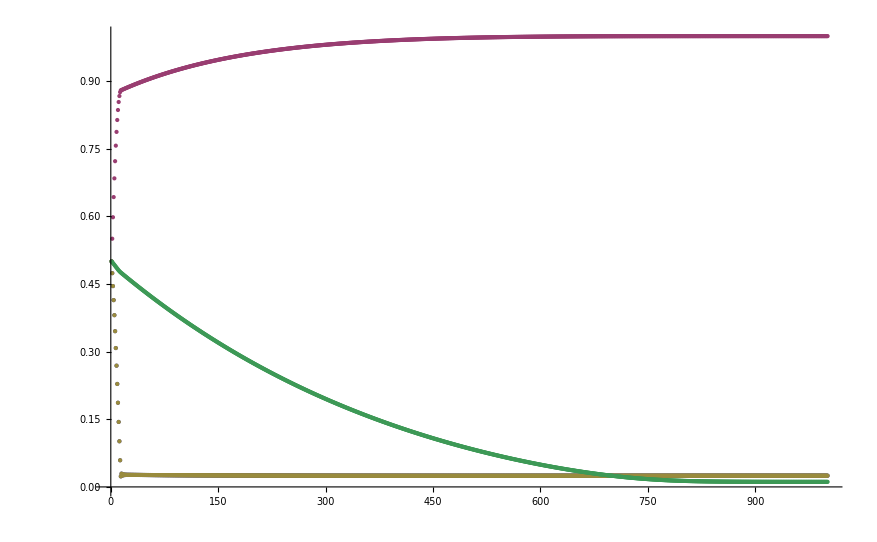

```mathematica
ListPlot[Map[Block[{i=#}, Map[#[[i]]&,results ]]&,Range[1,4]]]
```